```mathematica
01 Feb 2021
ODE solving
```

2021 Feb

ODE solving

```mathematica
(*Just to show the derivative in a traditional form*)
```

```mathematica
Clear["Global`*"];
```

```mathematica
pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

```mathematica
Eq2[t,x]= D[pi[t,x], t,t]  - D[pi[t,x], x] D[pi[t,x], x] ;
```

```mathematica
Eq2[t,x]==0//pdConv
```

(∂^2 pi(t,x))/(∂t^2)-((∂pi(t,x))/(∂x))^2==0

```mathematica
assum2[t_,x_]:= a[t] x^2;
```

```mathematica
NewEq2=Block[{pi},pi[t_,x_]:=assum2[t,x];Eq2[t,x]]
```

-4 x^2 a[t]^2+x^2 a''[t]

```mathematica
For[i=1,i<6,i++,Print[ToString[x^i,StandardForm]<>": ",Coefficient[NewEq2,x^i]]]
```

x: 0

x^2: -4 a[t]^2+a''[t]

x^3: 0

x^4: 0

x^5: 0

```mathematica
Solvind the full equation π^(..) +Lin=NL
```

```mathematica
(*Definition of Ψ and the linear term*)
```

```mathematica
π[t,x]+Φ
```

Φ+π[t,x]

```mathematica
π//N
```

3.14159

```mathematica
psi[τ_,x_]:= ψ2[τ] x^2;
```

```mathematica
(*L[t_,x_] := 2/t(1-3w)∂_t pi[t,x] + (-2/t^2-3w 4/t^2+3 cs2 6/t^2)pi[t,x]+6/t(w-cs2)Ψ[x]-cs2∂_(x,x) pi[t,x];*)
L[τ_,x_] := Subscript[l, πd][τ]D[pi[τ,x], τ] + Subscript[l, ππ][τ]pi[τ,x]+Subscript[l, Ψ][τ] ψ[τ,x]+Subscript[l, Ψd][τ] D[ψ[τ,x], τ]+Subscript[l, πpp][τ]D[pi[τ,x], x,x];
```

```mathematica
Print[L[τ,r]//pdConv]
```

pdConv[pi[τ,r] l_ππ[τ]+ψ[τ,r] l_Ψ[τ]+l_πpp[τ] pi^(0,2)[τ,r]+l_πd[τ] pi^(1,0)[τ,r]+l_Ψd[τ] ψ^(1,0)[τ,r]]

```mathematica
(*Definition of non-linear term*)
```

```mathematica
NonLin[τ_,x_]:= Subscript[ν, πpπp][τ] (D[pi[τ,x], x])^2 +Subscript[ν, πpπpd][τ]D[pi[τ,x], x]D[pi[τ,x], τ,x] + Subscript[ν, ππpp][τ] pi[τ,x]D[pi[τ,x], x,x]+Subscript[ν, πdπpp][τ] D[pi[τ,x], τ] D[pi[τ,x], x,x]+Subscript[ν, Ψπpp][τ] Ψ[τ,x] D[pi[τ,x], x,x]+Subscript[ν, Ψpπp][τ] D[Ψ[τ,x], x]D[pi[τ,x], x]+Subscript[ν, πpπpπpp][τ](D[pi[τ,x], x])^2 D[pi[τ,x], x,x];
```

```mathematica
(*Printing non-linear terms and checked *)
```

```mathematica
Print[NonLin[τ,x]//pdConv];
```

pdConv[ν_πpπp[τ] (pi^(0,1)[τ,x])^2+ν_Ψpπp[τ] pi^(0,1)[τ,x] Ψ^(0,1)[τ,x]+pi[τ,x] ν_ππpp[τ] pi^(0,2)[τ,x]+Ψ[τ,x] ν_Ψπpp[τ] pi^(0,2)[τ,x]+ν_πpπpπpp[τ] (pi^(0,1)[τ,x])^2 pi^(0,2)[τ,x]+ν_πdπpp[τ] pi^(0,2)[τ,x] pi^(1,0)[τ,x]+ν_πpπpd[τ] pi^(0,1)[τ,x] pi^(1,1)[τ,x]]

```mathematica
The full equation without linear terms
```

equation full linear terms The without

```mathematica
Eq[t_,x_]:= D[pi[t,x], t,t]+1*L[t,x]-NonLin[t,x];
```

```mathematica
Print[Eq[τ,x]//pdConv];
```

-ν_πpπpd(τ) (∂pi(τ,x))/(∂x) (∂^2 pi(τ,x))/(∂τ ∂x)+l_πpp(τ) (∂^2 pi(τ,x))/(∂x^2)+l_πd(τ) (∂pi(τ,x))/(∂τ)+l_ππ(τ) pi(τ,x)+l_Ψ(τ) ψ(τ,x)+l_Ψd(τ) (∂ψ(τ,x))/(∂τ)-ν_πdπpp(τ) (∂pi(τ,x))/(∂τ) (∂^2 pi(τ,x))/(∂x^2)-ν_ππpp(τ) pi(τ,x) (∂^2 pi(τ,x))/(∂x^2)-ν_πpπpπpp(τ) ((∂pi(τ,x))/(∂x))^2 (∂^2 pi(τ,x))/(∂x^2)+x^2 ψ2(τ) ν_Ψπpp(τ) (-(∂^2 pi(τ,x))/(∂x^2))-ν_πpπp(τ) ((∂pi(τ,x))/(∂x))^2-2 x ψ2(τ) ν_Ψpπp(τ) (∂pi(τ,x))/(∂x)+(∂^2 pi(τ,x))/(∂τ^2)

```mathematica
assum[t_,x_] :=  Subscript[u, 2][t] x^2;
```

```mathematica
NewEq=Block[{pi},pi[τ_,x_]:= Subscript[u, 2][τ] x^2;Eq[τ,x]]
For[i=0,i<5,i++,If[i==0, Print["x^0:"NewEq /.{x->0}]];If[i!=0,Print[ToString[x^i,StandardForm]<>": ",Coefficient[NewEq,x^i]]]]
```

ψ[τ,x] l_Ψ[τ]+2 l_πpp[τ] u_2[τ]+x^2 l_ππ[τ] u_2[τ]-4 x^2 u_2[τ]^2 ν_πpπp[τ]-8 x^2 u_2[τ]^3 ν_πpπpπpp[τ]-2 x^2 u_2[τ]^2 ν_ππpp[τ]-4 x^2 ψ2[τ] u_2[τ] ν_Ψpπp[τ]-2 x^2 ψ2[τ] u_2[τ] ν_Ψπpp[τ]+x^2 l_πd[τ] u_2'[τ]-2 x^2 u_2[τ] ν_πdπpp[τ] u_2'[τ]-4 x^2 u_2[τ] ν_πpπpd[τ] u_2'[τ]+x^2 u_2''[τ]+l_Ψd[τ] ψ^(1,0)[τ,x]

x^0: (ψ[τ,0] l_Ψ[τ]+2 l_πpp[τ] u_2[τ]+l_Ψd[τ] ψ^(1,0)[τ,0])

x: 0

x^2: l_ππ[τ] u_2[τ]-4 u_2[τ]^2 ν_πpπp[τ]-8 u_2[τ]^3 ν_πpπpπpp[τ]-2 u_2[τ]^2 ν_ππpp[τ]-4 ψ2[τ] u_2[τ] ν_Ψpπp[τ]-2 ψ2[τ] u_2[τ] ν_Ψπpp[τ]+l_πd[τ] u_2'[τ]-2 u_2[τ] ν_πdπpp[τ] u_2'[τ]-4 u_2[τ] ν_πpπpd[τ] u_2'[τ]+u_2''[τ]

x^3: 0

x^4: 0

```mathematica
For[i=0,i<5,i++,If[i==0, Print["x^0:"NewEq /.{x->0}]];If[i!=0,Print[ToString[x^i,StandardForm]<>": ",Coefficient[NewEq,x^i]]]]
```

x^0: (ψ[τ,0] l_Ψ[τ]+l_ππ[τ] u_0[τ]+2 l_πpp[τ] u_2[τ]-u_1[τ]^2 ν_πpπp[τ]-2 u_1[τ]^2 u_2[τ] ν_πpπpπpp[τ]-2 u_0[τ] u_2[τ] ν_ππpp[τ]-ψ1[τ] u_1[τ] ν_Ψpπp[τ]-2 ψ0[τ] u_2[τ] ν_Ψπpp[τ]+l_πd[τ] u_0'[τ]-2 u_2[τ] ν_πdπpp[τ] u_0'[τ]-u_1[τ] ν_πpπpd[τ] u_1'[τ]+u_0''[τ]+l_Ψd[τ] ψ^(1,0)[τ,0])

x: l_ππ[τ] u_1[τ]+6 l_πpp[τ] u_3[τ]-4 u_1[τ] u_2[τ] ν_πpπp[τ]-8 u_1[τ] u_2[τ]^2 ν_πpπpπpp[τ]-6 u_1[τ]^2 u_3[τ] ν_πpπpπpp[τ]-2 u_1[τ] u_2[τ] ν_ππpp[τ]-6 u_0[τ] u_3[τ] ν_ππpp[τ]-2 ψ2[τ] u_1[τ] ν_Ψpπp[τ]-2 ψ1[τ] u_2[τ] ν_Ψpπp[τ]-2 ψ1[τ] u_2[τ] ν_Ψπpp[τ]-6 ψ0[τ] u_3[τ] ν_Ψπpp[τ]-6 u_3[τ] ν_πdπpp[τ] u_0'[τ]+l_πd[τ] u_1'[τ]-2 u_2[τ] ν_πdπpp[τ] u_1'[τ]-2 u_2[τ] ν_πpπpd[τ] u_1'[τ]-2 u_1[τ] ν_πpπpd[τ] u_2'[τ]+u_1''[τ]

x^2: l_ππ[τ] u_2[τ]+12 l_πpp[τ] u_4[τ]-4 u_2[τ]^2 ν_πpπp[τ]-6 u_1[τ] u_3[τ] ν_πpπp[τ]-8 u_2[τ]^3 ν_πpπpπpp[τ]-36 u_1[τ] u_2[τ] u_3[τ] ν_πpπpπpp[τ]-12 u_1[τ]^2 u_4[τ] ν_πpπpπpp[τ]-2 u_2[τ]^2 ν_ππpp[τ]-6 u_1[τ] u_3[τ] ν_ππpp[τ]-12 u_0[τ] u_4[τ] ν_ππpp[τ]-3 ψ3[τ] u_1[τ] ν_Ψpπp[τ]-4 ψ2[τ] u_2[τ] ν_Ψpπp[τ]-3 ψ1[τ] u_3[τ] ν_Ψpπp[τ]-2 ψ2[τ] u_2[τ] ν_Ψπpp[τ]-6 ψ1[τ] u_3[τ] ν_Ψπpp[τ]-12 ψ0[τ] u_4[τ] ν_Ψπpp[τ]-12 u_4[τ] ν_πdπpp[τ] u_0'[τ]-6 u_3[τ] ν_πdπpp[τ] u_1'[τ]-3 u_3[τ] ν_πpπpd[τ] u_1'[τ]+l_πd[τ] u_2'[τ]-2 u_2[τ] ν_πdπpp[τ] u_2'[τ]-4 u_2[τ] ν_πpπpd[τ] u_2'[τ]-3 u_1[τ] ν_πpπpd[τ] u_3'[τ]+u_2''[τ]

x^3: l_ππ[τ] u_3[τ]-12 u_2[τ] u_3[τ] ν_πpπp[τ]-8 u_1[τ] u_4[τ] ν_πpπp[τ]-48 u_2[τ]^2 u_3[τ] ν_πpπpπpp[τ]-36 u_1[τ] u_3[τ]^2 ν_πpπpπpp[τ]-64 u_1[τ] u_2[τ] u_4[τ] ν_πpπpπpp[τ]-8 u_2[τ] u_3[τ] ν_ππpp[τ]-12 u_1[τ] u_4[τ] ν_ππpp[τ]-4 ψ4[τ] u_1[τ] ν_Ψpπp[τ]-6 ψ3[τ] u_2[τ] ν_Ψpπp[τ]-6 ψ2[τ] u_3[τ] ν_Ψpπp[τ]-4 ψ1[τ] u_4[τ] ν_Ψpπp[τ]-2 ψ3[τ] u_2[τ] ν_Ψπpp[τ]-6 ψ2[τ] u_3[τ] ν_Ψπpp[τ]-12 ψ1[τ] u_4[τ] ν_Ψπpp[τ]-12 u_4[τ] ν_πdπpp[τ] u_1'[τ]-4 u_4[τ] ν_πpπpd[τ] u_1'[τ]-6 u_3[τ] ν_πdπpp[τ] u_2'[τ]-6 u_3[τ] ν_πpπpd[τ] u_2'[τ]+l_πd[τ] u_3'[τ]-2 u_2[τ] ν_πdπpp[τ] u_3'[τ]-6 u_2[τ] ν_πpπpd[τ] u_3'[τ]-4 u_1[τ] ν_πpπpd[τ] u_4'[τ]+u_3''[τ]

x^4: l_ππ[τ] u_4[τ]-9 u_3[τ]^2 ν_πpπp[τ]-16 u_2[τ] u_4[τ] ν_πpπp[τ]-90 u_2[τ] u_3[τ]^2 ν_πpπpπpp[τ]-80 u_2[τ]^2 u_4[τ] ν_πpπpπpp[τ]-120 u_1[τ] u_3[τ] u_4[τ] ν_πpπpπpp[τ]-6 u_3[τ]^2 ν_ππpp[τ]-14 u_2[τ] u_4[τ] ν_ππpp[τ]-8 ψ4[τ] u_2[τ] ν_Ψpπp[τ]-9 ψ3[τ] u_3[τ] ν_Ψpπp[τ]-8 ψ2[τ] u_4[τ] ν_Ψpπp[τ]-2 ψ4[τ] u_2[τ] ν_Ψπpp[τ]-6 ψ3[τ] u_3[τ] ν_Ψπpp[τ]-12 ψ2[τ] u_4[τ] ν_Ψπpp[τ]-12 u_4[τ] ν_πdπpp[τ] u_2'[τ]-8 u_4[τ] ν_πpπpd[τ] u_2'[τ]-6 u_3[τ] ν_πdπpp[τ] u_3'[τ]-9 u_3[τ] ν_πpπpd[τ] u_3'[τ]+l_πd[τ] u_4'[τ]-2 u_2[τ] ν_πdπpp[τ] u_4'[τ]-8 u_2[τ] ν_πpπpd[τ] u_4'[τ]+u_4''[τ]

```mathematica
Cosmology functions:
```

0.-0.000015003 Η[τ,0.0691023,0.31,0.68991,-0.5,9/100000]+0.000059994 u_2[τ]+(1.5003 Η[τ,0.0691023,0.31,0.68991,-0.5,9/100000]^2+0.9997 Ηprime[τ,0.0691023,0.31,0.68991,-0.5,9/100000]) u_2[τ]-8.9985 Η[τ,0.0691023,0.31,0.68991,-0.5,9/100000] u_2[τ]^2+11.9988 u_2[τ]^3-16.497 Η[τ,0.0691023,0.31,0.68991,-0.5,9/100000] u_1[τ] u_3[τ]+53.9946 u_1[τ] u_2[τ] u_3[τ]-0.0012 u_4[τ]-11.997 Η[τ,0.0691023,0.31,0.68991,-0.5,9/100000] u_0[τ] u_4[τ]+17.9982 u_1[τ]^2 u_4[τ]-1.0003 ψ2'[τ]-11.9988 u_4[τ] u_0'[τ]-11.9988 u_3[τ] u_1'[τ]+2.5 Η[τ,0.0691023,0.31,0.68991,-0.5,9/100000] u_2'[τ]-9.999 u_2[τ] u_2'[τ]-5.9994 u_1[τ] u_3'[τ]+u_2''[τ]

```mathematica
(*scale factor in terms of the Redshift  *)
scalfactor[z_]:=1/(1+z);
redshift[a_]:=1/a-1;
```

```mathematica
(*Function to compute conformal time for a given redshift*)
tau[zs_,H0_,Ωm_,Ωd_,w_,Ωr_]:=NIntegrate[H0^-1/(√(Ωd(1+z)^(3(1+w)) +Ωm (1+z)^3+Ωr(1+z)^4)),{z,zs,∞},PrecisionGoal->12,AccuracyGoal->12]
```

```mathematica
(*Function to compute Physical time for a given redshift = (a'(tau))/a*)
time[zs_,H0_,Ωm_,Ωd_,w_,Ωr_]:=NIntegrate[H0^-1/((1+z)√(Ωd(1+z)^(3(1+w)) +Ωm (1+z)^3+Ωr(1+z)^4)),{z,zs,∞}]
```

```mathematica
(*Physical Hubble Function at a given redshift = (ȧ)/a *)
PhysicalHubble[z_,H0_,Ωm_,Ωd_,w_,Ωr_]:=H0 √(Ωd(1+z)^(3(1+w)) +Ωm (1+z)^3+Ωr(1+z)^4)
```

```mathematica
(*Conformal Hubble Function at a given redshift *)
ConformalHubble[z_,H0_,Ωm_,Ωd_,w_,Ωr_]:=H0 √(Ωd(1+z)^(1+3 w) +Ωm (1+z)+Ωr(1+z)^2)
```

```mathematica
(*Conformal Hubble Function at a given redshift *)
ConformalHubble[τ_,H0_,Ωm_,Ωd_,w_,Ωr_]:=H0 √(Ωd(1+z)^(1+3 w) +Ωm (1+z)+Ωr(1+z)^2)
```

```mathematica
(*Time derivative of the Conformal Hubble Function at a given redshift = (ȧ)/a *)
ConformalHubblePrime[z_,H0_,Ωm_,Ωd_,w_,Ωr_]:=D[ConformalHubble[z,H0,Ωm,Ωd,w,Ωr],z]*(-(1+z)^2)*ConformalHubble[z,H0,Ωm,Ωd,w,Ωr]*1/(1+z);  (* (d HH)/dtau = dH/dz  dz/da da/dtau*)
```

# Cosmological settings

```mathematica
w = -0.5;
cs2=0.0001;
H0=0.0691023;
Ωm=0.31;
Ωr=9 10^-5;
Ωd=1-Ωm-Ωr;
```

```mathematica
Solving the coupled ODEs:
```

```mathematica
Linear coeficients definition:
```

```mathematica
Subscript[l, πd][τ] = (1-3 w) Η[τ,H0,Ωm,Ωd,w,Ωr];
Subscript[l, ππ][τ] = (1-3cs2) Ηprime[τ,H0,Ωm,Ωd,w,Ωr] + 3(cs2-w) Η[τ,H0,Ωm,Ωd,w,Ωr]^2;
Subscript[l, Ψ][τ] = 3(w-cs2) Η[τ,H0,Ωm,Ωd,w,Ωr];
Subscript[l, Ψd][τ] = -(1+3cs2);
Subscript[l, πpp][τ] = -cs2;
```

```mathematica
Non-linear coeficients definition:
```

```mathematica
Subscript[ν, πpπp][τ]  = (-Η[τ,H0,Ωm,Ωd,w,Ωr])/2 (5 cs2 +3 w -2);
Subscript[ν, πpπpd][τ] = 2(1-cs2);
Subscript[ν, ππpp][τ] = -Η[τ,H0,Ωm,Ωd,w,Ωr]( (cs2-1) + 3 cs2(1+w));
Subscript[ν, πdπpp][τ] = -(cs2-1);
Subscript[ν, Ψπpp][τ] = (cs2-1);
Subscript[ν, Ψpπp][τ] = (cs2-1);
Subscript[ν, πpπpπpp][τ] = 3/2(cs2-1);
```

Set of equations

```mathematica
Psiequation[ψ_,τ_,Ωm_,Ωd_,w_,Ωr_]:= ψ''[τ] + 3 Η[τ,H0,Ωm,Ωd,w,Ωr]ψ'[τ]+((2-(3 Ωm)/(2 Ωm + 2 Ωd a[τ]^(-3 w)+ 2 Ωr a[τ]^-1))Η[τ,H0,Ωm,Ωd,w,Ωr]^2+ Ηprime[τ,H0,Ωm,Ωd,w,Ωr])ψ[τ];

Eqψ0 = ψ0''[τ] + 3 Η[τ,H0,Ωm,Ωd,w,Ωr]ψ0'[τ]+((2-(3 Ωm)/(2 Ωm + 2 Ωd a[τ]^(-3 w)+ 2 Ωr a[τ]^-1))Η[τ,H0,Ωm,Ωd,w,Ωr]^2+ Ηprime[τ,H0,Ωm,Ωd,w,Ωr])ψ0[τ];
Eqψ1 = ψ1''[τ] + 3 Η[τ,H0,Ωm,Ωd,w,Ωr]ψ1'[τ]+((2-(3 Ωm)/(2 Ωm + 2 Ωd a[τ]^(-3 w)+ 2 Ωr a[τ]^-1))Η[τ,H0,Ωm,Ωd,w,Ωr]^2+ Ηprime[τ,H0,Ωm,Ωd,w,Ωr])ψ1[τ];
Eqψ2 = ψ2''[τ] + 3 Η[τ,H0,Ωm,Ωd,w,Ωr]ψ2'[τ]+((2-(3 Ωm)/(2 Ωm + 2 Ωd a[τ]^(-3 w)+ 2 Ωr a[τ]^-1))Η[τ,H0,Ωm,Ωd,w,Ωr]^2+ Ηprime[τ,H0,Ωm,Ωd,w,Ωr])ψ2[τ];
Eqψ3 = ψ3''[τ] + 3 Η[τ,H0,Ωm,Ωd,w,Ωr]ψ3'[τ]+((2-(3 Ωm)/(2 Ωm + 2 Ωd a[τ]^(-3 w)+ 2 Ωr a[τ]^-1))Η[τ,H0,Ωm,Ωd,w,Ωr]^2+ Ηprime[τ,H0,Ωm,Ωd,w,Ωr])ψ3[τ];
Eqψ4 = ψ4''[τ] + 3 Η[τ,H0,Ωm,Ωd,w,Ωr]ψ4'[τ]+((2-(3 Ωm)/(2 Ωm + 2 Ωd a[τ]^(-3 w)+ 2 Ωr a[τ]^-1))Η[τ,H0,Ωm,Ωd,w,Ωr]^2+ Ηprime[τ,H0,Ωm,Ωd,w,Ωr])ψ4[τ];
eqn0=NewEq/.{x->0};
eqn1=Coefficient[NewEq,x^1];
eqn2=Coefficient[NewEq,x^2]
eqn3=Coefficient[NewEq,x^3];
eqn4=Coefficient[NewEq,x^4];
```

(1.5003 Η[τ,0.0691023,0.31,0.68991,-0.5,9/100000]^2+0.9997 Ηprime[τ,0.0691023,0.31,0.68991,-0.5,9/100000]) u_2[τ]+5.9994 ψ2[τ] u_2[τ]-8.9985 Η[τ,0.0691023,0.31,0.68991,-0.5,9/100000] u_2[τ]^2+11.9988 u_2[τ]^3+2.5 Η[τ,0.0691023,0.31,0.68991,-0.5,9/100000] u_2'[τ]-9.999 u_2[τ] u_2'[τ]+u_2''[τ]

```mathematica
eqn2
```

0.-0.000030006/τ+0.000059994 u_2[τ]+(4.0018 u_2[τ])/τ^2-(17.997 u_2[τ]^2)/τ+11.9988 u_2[τ]^3-(32.994 u_1[τ] u_3[τ])/τ+53.9946 u_1[τ] u_2[τ] u_3[τ]-0.0012 u_4[τ]-(23.994 u_0[τ] u_4[τ])/τ+17.9982 u_1[τ]^2 u_4[τ]-11.9988 u_4[τ] u_0'[τ]-11.9988 u_3[τ] u_1'[τ]+(5. u_2'[τ])/τ-9.999 u_2[τ] u_2'[τ]-5.9994 u_1[τ] u_3'[τ]+u_2''[τ]

## Assumptions

```mathematica
assumptions = {Η[τ,H0,Ωm,Ωd,w,Ωr]->2/τ,Ηprime[τ,H0,Ωm,Ωd,w,Ωr]->-2/τ^2, ψ0[τ]->0,ψ1[τ]->0,ψ2[τ]->-10^-2,ψ3[τ]->0,ψ4[τ]->0, ψ0'[τ]->0,ψ1'[τ]->0,ψ2'[τ]->0,ψ3'[τ]->0,ψ4'[τ]->0};
(*ψ0[τ]:=0
ψ1[τ]:=0
ψ2[τ]:=10^-5
ψ3[τ]:=0
ψ4[τ]:=0*)
eqn0 = eqn0/.assumptions;
eqn1 = eqn1/.assumptions;
eqn2 = eqn2/.assumptions;
eqn3 = eqn3/.assumptions;
eqn4 = eqn4/.assumptions;
```

```mathematica
τini = tau[1000,H0,Ωm,Ωd,w,Ωr];
τfin = tau[0,H0,Ωm,Ωd,w,Ωr];

s=NDSolve[{eqn0==0,eqn1==0, eqn2==0, eqn3==0, eqn4==0,Subscript[u, 2][τini]==0.0,Subscript[u, 2]'[τini]==0.0},{Subscript[u, 2][τ],Subscript[u, 2]'[τ]},{τ,τini,τfin}]
```

NDSolve::deqn: Equation or list of equations expected instead of True in the first argument {0.-(3.0006 ψ[τ,0])/τ-0.0002 u_2[τ]-1.0003 ψ^(1,0)[τ,0]==0,True,-0.059994 u_2[τ]+(4.0018 u_2[τ])/τ^2-(17.997 u_2[τ]^2)/τ+11.9988 u_2[τ]^3+(5. u_2'[τ])/τ-9.999 u_2[τ] u_2'[τ]+u_2''[τ]==0,True,True,u_2[tau[1000,0.0691023,0.31,0.68991,-0.5,9/100000]]==0.,u_2'[tau[1000,0.0691023,0.31,0.68991,-0.5,9/100000]]==0.}.

NDSolve[{0.-(3.0006 ψ[τ,0])/τ-0.0002 u_2[τ]-1.0003 ψ^(1,0)[τ,0]==0,True,-0.059994 u_2[τ]+(4.0018 u_2[τ])/τ^2-(17.997 u_2[τ]^2)/τ+11.9988 u_2[τ]^3+(5. u_2'[τ])/τ-9.999 u_2[τ] u_2'[τ]+u_2''[τ]==0,True,True,u_2[tau[1000,0.0691023,0.31,0.68991,-0.5,9/100000]]==0.,u_2'[tau[1000,0.0691023,0.31,0.68991,-0.5,9/100000]]==0.},{u_2[τ],u_2'[τ]},{τ,tau[1000,0.0691023,0.31,0.68991,-0.5,9/100000],tau[0,0.0691023,0.31,0.68991,-0.5,9/100000]}]

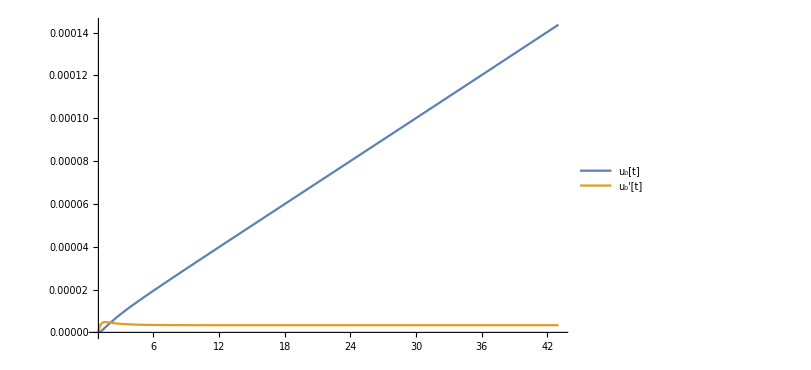

```mathematica
plt = Plot[Evaluate[{Subscript[u, 2][τ],Subscript[u, 2]'[τ]}/.s],{τ,τini,τfin},PlotRange->Full,PlotLegends->{"u_0[t]","u_0'[t]"}, PlotStyle->Thick, ImageSize->600]
```

```mathematica
{Subscript[u, 2][τ],Subscript[u, 2]'[τ]}/.s/.τ->1
```

{{5.84634×10^-9,5.27471×10^-7}}

```mathematica
τini = tau[1000,H0,Ωm,Ωd,w,Ωr]
τfin = tau[0,H0,Ωm,Ωd,w,Ωr]
```

0.980812

43.0056